# Optimal hedging

This file contains prototype functions. For running the actual optimal hedges see NIGRiskMeasures_PeriodicCalibration.nb.

## Introduction

Use risk measures from Barbi and Romagnoli to obtain optimal hedge:
VaR, ES at 95%, 99% levels (possibly 99.5%) and ERM with k=10.
	
-Graphics-

Idea: Use walk forward method (Lopez da Prado), by calibrating on one year of data, then hedging out-of-sample for one month.

## Modules

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
NIGCDFi[α_?NumericQ,β_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,NIGCDF[x,α,β]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
Rho[α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{μ1,δ1,Fi},
μ1=μs[α,β];
δ1=δs[α,β];
Fi=FNIGi[α,β,μ1,δ1-δ];
12 NIntegrate[Fi[x-z] Fi[y-z] fNIG[z,α,β,0,δ]NIGPDF[x,α,β] NIGPDF[y,α,β], {z,-∞, ∞},{x,-∞, ∞},{y,-∞, ∞},PrecisionGoal->2]-3
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

-Graphics-

```mathematica
Clear[hatQ]
```

```mathematica
hatQ[p_,s_]:=Module[{k},
k=Ceiling[(Length[s]p)+1];
Sort[s]⟦Min[k,Length[s]]⟧
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β] ;
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,0.1,1},{β,-0.1,0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1]];
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

## Read BTC data

```mathematica
data=Import[NotebookDirectory[]<> "../processed_data/btc_future_crix.csv"];
data = Import[NotebookDirectory[] <> "../data/btc future and reference rate/coingecko_future.csv"];
```

```mathematica
(*rbtc=data⟦2;;All,12⟧;
rbrr=data⟦2;;All,13⟧;*)
```

```mathematica
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,5⟧;
```

```mathematica
Dimensions[data]
```

{679,6}

```mathematica
hatqd=Table[QDemp[q,data⟦2;;All,5⟧,data⟦2;;All,6⟧],{q,{0.05,0.1,0.9,0.95}}];target=Flatten[Join[{SpearmanRho[data⟦2;;All,5⟧,data⟦2;;All,6⟧]},hatqd]]
```

{0.90401,0.855457,0.825959,0.855457,0.766962}

```mathematica
const=Sin[1/6 target⟦1⟧ π] 2
```

0.911721

```mathematica
sol=calibrate[data⟦2;;All,5;;6⟧]
```

{0.768708,0.00389689,0.0671537,745.813}

```mathematica
{α0=sol[[1]],β0=sol[[2]],δ0=Sin[1/6 target⟦1⟧ π] 2 δs[α0,β0]}
```

{0.768708,0.00389689,0.70082}

```mathematica
r=Range[0.01, 0.99, 0.02];
Length[r]
```

50

```mathematica
target=Table[{q,QDemp[q,data⟦;;,5⟧,data⟦;;,6⟧]},{q,r}];
```

```mathematica
F1=FNIGi[α0,β0,μs[α0,β0], δ0-const δ0];
```

```mathematica
f= Table[{q,QD[q0, α0,β0,δ0,F1]/.q0->q}, {q,r}];
```

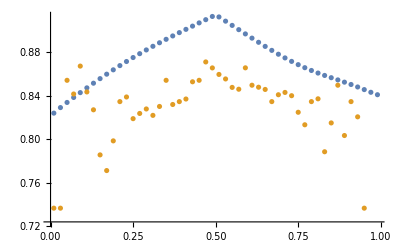

```mathematica
ListPlot[{f,target}]
```

```mathematica
Export[NotebookDirectory[] <> "data/QuantileDependence.csv", f]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data/QuantileDependence.csv

## Simulation

```mathematica
α=α0; 
β=β0;
δ=δ0;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
SeedRandom[123456];
n=50000;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
R[h_]:=(1-h) Z + Z1 - h Z2;
```

```mathematica
r=R[0.5];
```

```mathematica
Dimensions[r]
```

{50000}

Too slow

```mathematica
Timing[x1=Table[NIGCDF[X1[[k]],α,β], {k,1,100}];]
```

{2.1205,Null}

Too slow

```mathematica
Timing[x1=CDF[HyperbolicDistribution[-1/2,α,β,δs[α,β],μs[α,β]],X1⟦1;;100⟧];]
```

{2.13298,Null}

```mathematica
Timing[
usim = hatF[X1];
vsim = hatF[X2];
]
```

{99.7761,Null}

```mathematica
dbtc=EmpiricalDistribution[rbtc];
dbrr=EmpiricalDistribution[rbrr];
```

```mathematica
Timing[rs=InverseCDF[dbtc, usim];]
Timing[rf=InverseCDF[dbrr, vsim];]
```

{2.78728,Null}

{2.43063,Null}

```mathematica
Clear[r]
```

```mathematica
r[h_?NumericQ]:=rs -h rf;
```

### Minimum variance

```mathematica
sol=NMinimize[Variance[r[h]], h]
```

{0.000970674,{h→0.818378}}

```mathematica
Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf]
```

0.818378

```mathematica
minvar=h/.sol[[2]]
```

0.818378

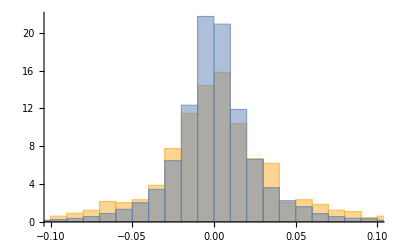

```mathematica
Histogram[{r[0], r[minvar]}, Automatic, "PDF"]
```

### Value-at-risk

```mathematica
NMinimize[-Quantile[r[h],0.01], h]
```

{0.0922205,{h→0.716052}}

```mathematica
NMinimize[-Quantile[r[h],0.05], h]
```

{0.0451603,{h→0.920594}}

### Expected Shortfall

```mathematica
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
ES[1,0.99]
```

0.138817

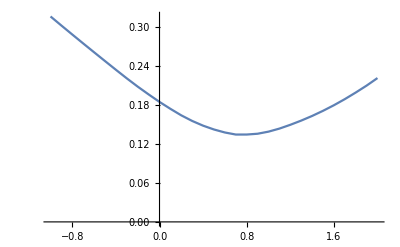

```mathematica
ListPlot[Table[{h,ES[h, 0.99]}, {h,-1,2, 0.1}],Joined->True]
```

```mathematica
NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h]
```

{0.134164,{h→0.738904}}

```mathematica
NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h]
```

{0.07682,{h→0.81092}}

### Spectral risk measure

```mathematica
k=10; (* parameter from Barbi Romagnoli *)
```

```mathematica
x=Range[1,100];
```

```mathematica
Quantile[x,0.025]
```

3

```mathematica
f[s_, p_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p]
```

```mathematica
SpectralRisk[h_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
Timing[NMinimize[SpectralRisk[h],h]]
```

{570.377,{0.0470412,{h→0.833294}}}

## Old stuff (attempt of numerical integration that did not work out properly)

```mathematica
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
```

```mathematica
NIGCDFi[α_?NumericQ,β_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μs[α,β],δs[α,β]];
b= InvFNIG[0.9999999,α,β,μs[α,β],δs[α,β]];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,NIGCDF[x,α,β]}, {x, r}]]
]
```

```mathematica
Fi=FNIGi[α0,β0,μs[α0,β0], δs[α0,β0]-δ0];
F2i = NIGCDFi[α0,β0];
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[ListQ[x],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}],
N[1/(n+1) Length[Select[s, #1≤x&]]]
]
]
```

```mathematica
h=1;
x=1;
Timing[NIntegrate[Fi[hatF[1/h(hatQ[F2i[z+z1],rbtc]-x),rbrr]-z]NIGPDF[z,α0,β0] fNIG[z1,α0,β0,μs[α0,β0],δs[α0,β0]-δ0],{z,-∞,∞},{z1,-∞,∞}]]
```

{1.10894,0.520432}

```mathematica
h=1;
x=0.5;
Timing[NIntegrate[(hatQ[NIGCDF[z+z1,α0,β0],rbtc]-x)NIGPDF[z,α0,β0] ,{z,-∞,∞},{z1,-∞,∞}]]
```

Part::pkspec1: The expression min(645,1+645) cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
h=1;
Clear[x]
Timing[NIntegrate[FNIG[hatF[1/h(hatQ[NIGCDF[z+z1,α0,β0],rbtc]-x),rbrr]-z,α0,β0,μs[α0,β0], δs[α0,β0]-δ0] NIGPDF[z,α0,β0] fNIG[z1,α0,β0,μs[α0,β0],δs[α0,β0]-δ0],{z,-∞,∞},{z1,-∞,∞}]]
```

Part::pkspec1: The expression min(645,1+645) cannot be used as a part specification.

$Aborted

```mathematica
CDF[HyperbolicDistribution[-1/2, 0.772993, 0.0293319, 0.771324, -0.0292896],1]
```

0.887107

```mathematica
hatqd=Table[QDemp[q,data⟦2;;All,12⟧,data⟦2;;All,13⟧],{q,{0.05,0.1,0.9,0.95}}];target=Flatten[Join[{SpearmanRho[data⟦2;;All,12⟧,data⟦2;;All,13⟧]},hatqd]]
```

Part::take: Cannot take positions 2 through -1 in data.

Part::pkspec1: The expression data cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::take: Cannot take positions 2 through -1 in data.

General::stop: Further output of Part::take will be suppressed during this calculation.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

{SpearmanRho[data⟦2;;All,12⟧,data⟦2;;All,13⟧],0.,0.,0.,0.}

```mathematica
α0=3.0836;
β0=-1.35137;
δ0=1.835933;
obj[α0,β0,δ0,target]
```

0.105295

```mathematica
α0=3.43896;
β0=0.616927;
δ0=3.39357;
obj[α0,β0,δ0,target]
```

0.119276

Parameters from calibration in NIGFactorCopula.nb

```mathematica
obj[3.1354,0.121548,2.53221,target]
```

0.10541

```mathematica
{Rho[α0,β0,δ0],(6 ArcSin[δ0/(2 δs[α0,β0])])/π,SpearmanRho[data⟦2;;All,12⟧,data⟦2;;All,13⟧]}
```

{0.0040047,0.000225856,0.733723}

```mathematica
F1=FNIGi[α0,β0,μs[α0,β0], δs[α0,β0]-δ0];
Table[QD[q0, α0,β0,δ0,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}]
```

{0.156193,0.22936,0.233946,0.161679}

```mathematica
Timing[t1=Table[{α,obj[α, β0,δ0,target]}, {α,2.6,5, 0.1}]];
```

```mathematica
Timing[t2=Table[{β,obj[α0,β,δ0,target]}, {β,-2,1, 0.1}]];
```

```mathematica
Timing[t3=Table[{δ,obj[α0,β0,δ,target]}, {δ,0.1,3.1, 0.25}]];
```

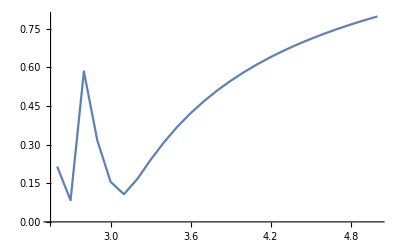
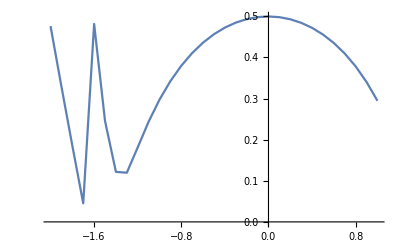
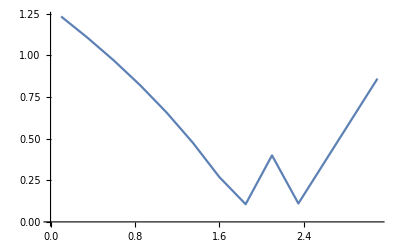

```mathematica
{ListPlot[t1, Joined->True], ListPlot[t2, Joined->True], ListPlot[t3, Joined->True]}
```

```mathematica
data[[1;;10,{1,12,13}]]
```

( | return_btc | return_brr
2020-09-04 | -0.0226425 | -0.0564519
2020-09-03 | -0.0667516 | -0.0409618
2020-09-02 | -0.0522745 | -0.0463652
2020-09-01 | 0.020076 | 0.0120735
2020-08-31 | 0.0174733 | 0.0233977
2020-08-28 | 0.0252517 | 0.0109912
2020-08-27 | -0.0252517 | -0.012727
2020-08-26 | 0.016472 | 0.00609231
2020-08-25 | -0.0427781 | -0.0313833)

```mathematica
dates=Reverse[data⟦2;;All,1⟧];
rbtc=Reverse[data⟦2;;All,12⟧];
rbrr=Reverse[data⟦2;;All,13⟧];
```

```mathematica
dates[[1;;252]][[{1,-1}]]
```

{2018-02-12,2019-02-14}

```mathematica
{Correlation[rbrr,rbtc], SpearmanRho[rbrr, rbtc]}
```

{0.788286,0.733723}

```mathematica
hatqd=Table[QDemp[q, rbrr, rbtc], {q,{0.05, 0.1, 0.9, 0.95}}]
```

{0.55814,0.635659,0.620155,0.589147}

```mathematica
target=Flatten[Join[{SpearmanRho[rbrr, rbtc]}, hatqd]]
```

{0.733723,0.55814,0.635659,0.620155,0.589147}

```mathematica
f=Flatten[Join[{HoldForm[(6 ArcSin[δ/(2 δs[α,β])])/π]}, Table[HoldForm[QD[q0, α,β,δ,F1]]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}]]]
```

{(6 sin^-1(δ/(2 δs(α,β))))/π,QD(0.05,α,β,δ,F1),QD(0.1,α,β,δ,F1),QD(0.9,α,β,δ,F1),QD(0.95,α,β,δ,F1)}

```mathematica
Clear[obj]
```

```mathematica
obj[α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{F1,f,q0,q},
If[δs[α,β]-δ<0,δ-δs[α,β],
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f=Flatten[Join[{(6 ArcSin[δ/(2 δs[α,β])])/π}, Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}]]];
Sqrt[Total[(target-f)^2]]
]
]
```

```mathematica
Timing[sol=NMinimize[{obj[α,β,δ],α>3 &&Abs[β]<α&&0< δ<Re[δs[α,β]]}, {α,β,δ}, Method->"SimulatedAnnealing", PrecisionGoal->2, AccuracyGoal->2]]
```

{985.592,{0.105795,{α→3.1354,β→0.121548,δ→2.53221}}}

```mathematica
obj[α0,-β0,δ0]
```

0.106757

```mathematica
{Rho[α0,β0,δ0],(6 ArcSin[δ0/(2 δs[α0,β0])])/π,SpearmanRho[rbrr,rbtc]}
```

{0.801063,0.795792,0.733723}

```mathematica
α0=α/.sol⟦2⟧;
β0=β/.sol⟦2⟧;
δ0=δ/.sol⟦2⟧;
```

```mathematica
δs[2.6,β0]-δ0
```

0.059268

```mathematica
δs[α0,β0]
```

3.12833

```mathematica
δ0/δs[α0,β0]
```

0.809445

```mathematica
Timing[t1=Table[{α,obj[α, β0,δ0]}, {α,2.6,5, 0.1}]];
```

```mathematica
Timing[t2=Table[{β,obj[α0,β,δ0]}, {β,-1,1, 0.1}]];
```

```mathematica
Timing[t3=Table[{δ,obj[α0,β0,δ]}, {δ,0.1,3.1, 0.25}]];
```

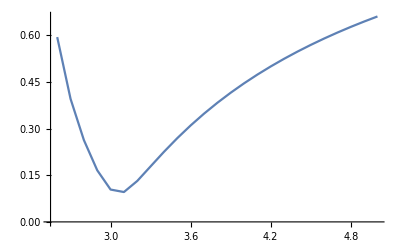
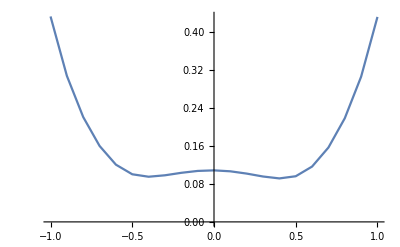
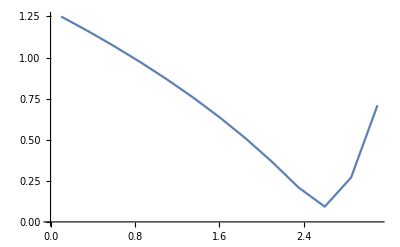

```mathematica
{ListPlot[t1, Joined->True], ListPlot[t2, Joined->True], ListPlot[t3, Joined->True]}
```

```mathematica
target
```

{0.733723,0.55814,0.635659,0.620155,0.589147}

```mathematica
F1=FNIGi[α0,β0,μs[α0,β0], δs[α0,β0]-δ0];
```

```mathematica
ReleaseHold[f/.{α->α0, β->β0, δ->δ0}]
```

{0.795792,0.529046,0.587149,0.589639,0.532498}

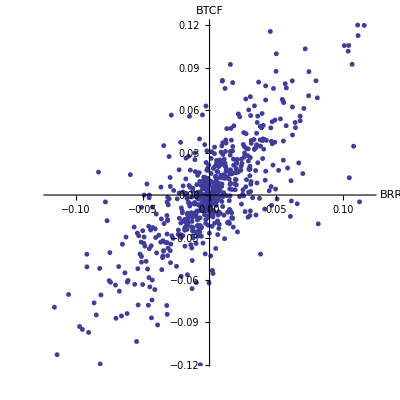

```mathematica
p=ListPlot[{rbrr,rbtc}ᵀ,PlotMarkers->{Automatic,5},PlotTheme->"Classic",BaseStyle->{FontSize->12},AspectRatio->1,AxesLabel->{"BRR", "BTCF"}]
```

```mathematica
Export[NotebookDirectory[] <>"../latex/_pics/scatter.pdf", p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/scatter.pdf

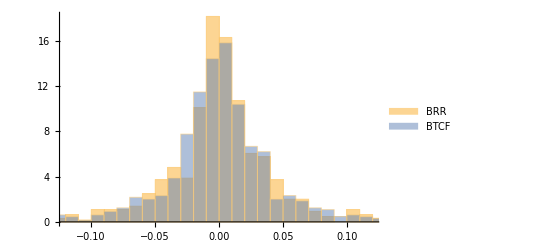

```mathematica
p=Histogram[{rbrr,rbtc}, Automatic, "PDF",ChartLegends->{"BRR", "BTCF"}]
```

```mathematica
Drbrr=EmpiricalDistribution[rbrr];
Drbtc=EmpiricalDistribution[rbtc];
```

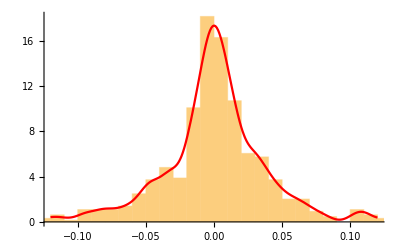
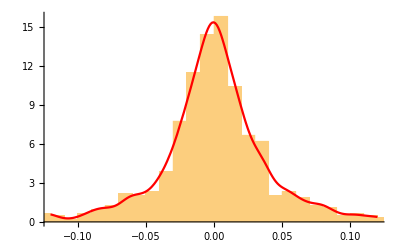

```mathematica
{p1=Show[
Histogram[rbrr, Automatic, "PDF"],
Plot[PDF[SmoothKernelDistribution[rbrr], x], {x,-0.12, 0.12},PlotStyle->Red]
],
p2=Show[
Histogram[rbtc, Automatic, "PDF"],
Plot[PDF[SmoothKernelDistribution[rbtc], x], {x,-0.12, 0.12},PlotStyle->Red]
]
}
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/rbrr.pdf",p1]
Export[NotebookDirectory[] <> "../latex/_pics/rbtc.pdf",p2]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rbrr.pdf

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rbtc.pdf

Make margins uniform using empirical distribution function (not smoothed version)

```mathematica
u=hatF[rbrr, rbrr];
v=hatF[rbtc, rbtc];
```

```mathematica
(*u=Table[CDF[Drbrr, rbrr[[i]]], {i,1,Length[rbrr]}];
v=Table[CDF[Drbtc, rbtc[[i]]], {i,1, Length[rbtc]}];*)
```

Drop largest sample (which has CDF of 1, messing up any sample mean-like computations)

```mathematica
(*u=DeleteCases[u, Max[u]];
v=DeleteCases[v, Max[v]];*)
```

Empirical copula

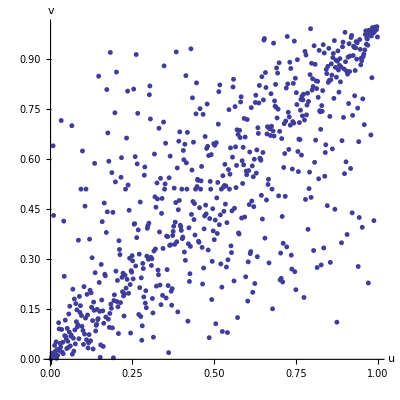

```mathematica
c1=ListPlot[{u,v}ᵀ,AxesLabel->{HoldForm[u], HoldForm[v]},PlotMarkers->{Automatic,5},PlotTheme->"Classic",BaseStyle->{FontSize->12},AspectRatio->1]
```

### Compare with simulated data

```mathematica
α=α0;
β=β0;
δ=δ0;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
SeedRandom[123456];
n=Length[rbrr];
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
{Mean[X1],Mean[X2]}
{Variance[X1], Variance[X2]}
```

{0.0207735,0.030492}

{0.902903,0.944557}

Correlation

```mathematica
N[{δ/δs[α,β],Correlation[X1,X2]}]
```

{0.809445,0.788985}

Rank correlation

```mathematica
N[{(6 ArcSin[δ/(2 δs[α,β])])/π,(6 ArcSin[1/2 Correlation[X1,X2]])/π,Rho[α,β,δ],SpearmanRho[X1,X2]}]
```

{0.795792,0.774477,0.801063,0.775153}

```mathematica
usim = hatF[X1,X1];
vsim = hatF[X2,X2];
```

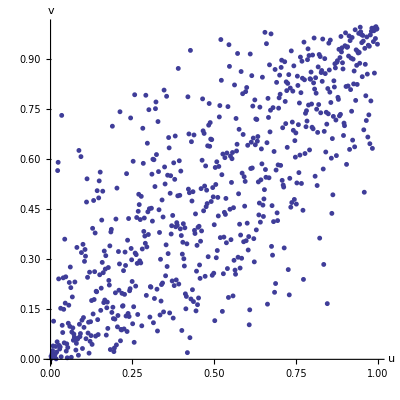

```mathematica
c2=ListPlot[{usim,vsim}ᵀ,AxesLabel->{HoldForm[u], HoldForm[v]},PlotMarkers->{Automatic,5},PlotTheme->"Classic",BaseStyle->{FontSize->12},AspectRatio->1]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copula_nig1.pdf", c1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copula_nig1.pdf

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copula_nig2.pdf", c2]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copula_nig2.pdf